```mathematica
datFileLocalChernlocation="/data/hstci/phase_diagram/";
```

```mathematica
paramsname="t0=1.0_t=1.0_NGridPts=31_Nplotpts=151_band1";
```

```mathematica
band1filename=StringJoin[paramsname,".csv"]
```

t0=1.0_t=1.0_NGridPts=31_Nplotpts=151_band1.csv

```mathematica
(*Import the CSV file*)
band1data=Import[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,band1filename]];
```

```mathematica
NN =Dimensions[band1data][[1]]
```

22801

```mathematica
totalChernData = Table[{band1data[[nn]][[1]],band1data[[nn]][[2]],band1data[[nn]][[3]]},{nn,1,NN}];
```

```mathematica
(*Extract x,y,and value columns*)
values=Table[totalChernData[[ii]][[3]],{ii,1,NN}];
```

```mathematica
rainbowColor=Function[x,Which[x>2,Red,x<-2,Purple,True,ColorData["Rainbow"][Rescale[x,{-2,2}]]]];
```

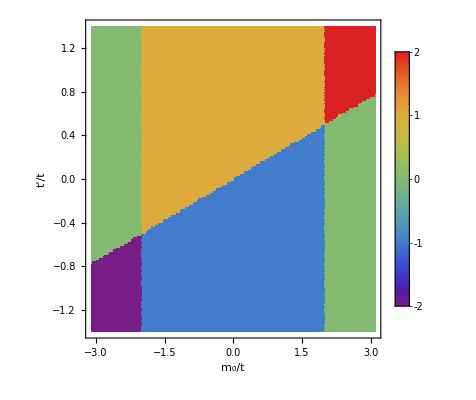

```mathematica
Show[ListDensityPlot[totalChernData,PlotRange->{All,All,All},ColorFunction->rainbowColor,ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{Black,FontSize->20}],Right],InterpolationOrder->0],Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},RotateLabel->False,FrameLabel->{"m_0/t","t'/t"},BaseStyle->20]
```

```mathematica
(** Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,paramsname,".pdf"],plt1]; **)
```

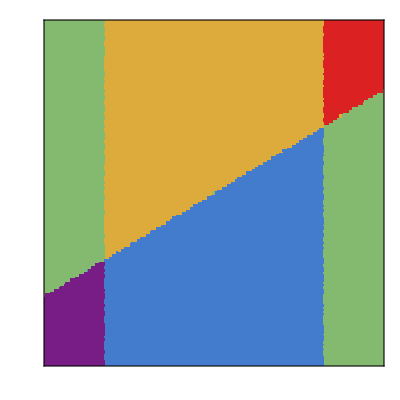

```mathematica
plt11=Show[ListDensityPlot[totalChernData,PlotRange->{All,All,All},ColorFunction->rainbowColor,ColorFunctionScaling->False,InterpolationOrder->0],Frame->True,FrameStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},RotateLabel->False,FrameLabel->{None,None},BaseStyle->20,
FrameTicks-> {{{{1.0,""},{0.5,""},{0.0,""},{-0.5,""},{-1.0,""}},None},{{{-3,""},{-2,""},{-1,""},{0,""},{1,""},{2,""},{3,""}},None}},
PlotRange-> {{-2.99,2.99},{-1.25,1.25}}]
```

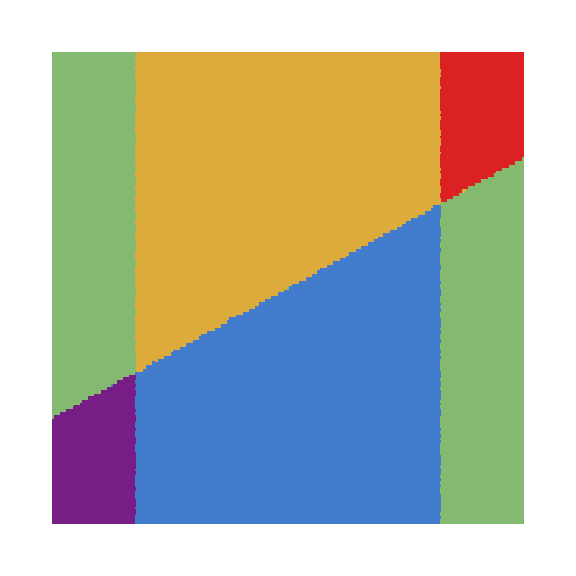

```mathematica
Show[ListDensityPlot[totalChernData,PlotRange->{All,All,All},ColorFunction->rainbowColor,ColorFunctionScaling->False,InterpolationOrder->0,Frame->False,(*Remove the frame here*)Axes->False,(*Optional:Remove axes if they are unwanted*)ImageSize->Large (*Adjusts the size to fit the plot more closely*)],BaseStyle->20]
```

```mathematica
Export[StringJoin[ParentDirectory[NotebookDirectory[]],datFileLocalChernlocation,paramsname,"_reduced.pdf"],Rasterize[plt11,ImageResolution->900]];
```